## Preliminaries

```mathematica
SetDirectory[NotebookDirectory[]]
dT=0.04;thick=Directive[Thick];
xTicks=Table[{j*10^-6,j,dT,{Thick,Black}},{j,-0.5,4,0.5}];
fontSize=18;
axesStyle={{Thick,Black},{Thick,Black}};
```

C:\Users\HILL\Documents\GitHub\thesis\figures\oscillator

## RefCurve_130143.txt.csv

```mathematica
data=Import["guiding01.csv","Dataset",HeaderLines->1];
t=Normal[data[All,"t"]];
ch1=Normal[data[All,"ch1"]];
ch2=Normal[data[All,"ch2"]];
ch3=Normal[data[All,"ch3"]];
```

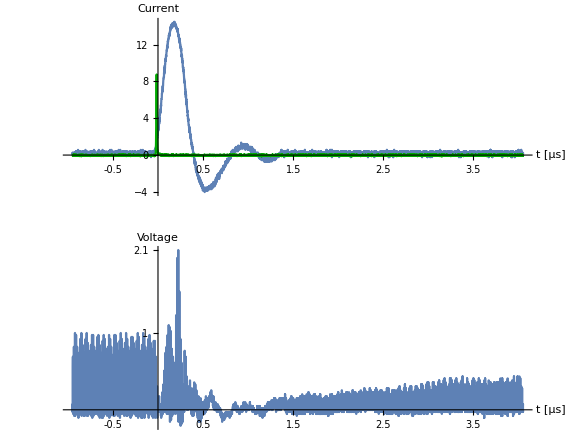

```mathematica
g1=GraphicsColumn[{
ListLinePlot[{Thread[{t,ch2}],Thread[{t,3RotateLeft[ch1,10]}]}
,AxesLabel->{"t [μs]","Current"}
,AxesStyle->axesStyle
,Ticks->{xTicks,Automatic}
,LabelStyle->Directive[Black,fontSize]
,PlotStyle->{Automatic,Darker[Green]}
,PlotRange->All
,AspectRatio->1/3]
,
ListLinePlot[Thread[{t,ch3}]
,AxesLabel->{"t [μs]","Voltage"}
,AxesStyle->axesStyle
,Ticks->{xTicks,{{Max[ch3⟦;;200⟧],1,dT,Black},{Max[ch3],NumberForm[Max[ch3]/Max[ch3⟦;;150⟧],2],dT,Black}}}
,LabelStyle->Directive[Black,fontSize]
,PlotRange->All
,AspectRatio->1/3]
},
GridLines->{Table[137+4i,{i,4}],None},GridLinesStyle->{{Dashed,Red},None},ImageSize->Large]
```

## 2020-02-02\RefCurve_191951.txt.Wfm

```mathematica
data=Import["guiding02.csv","Dataset",HeaderLines->1];
t=Normal[data[All,"t"]];
ch1=Normal[data[All,"ch1"]];
ch2=Normal[data[All,"ch2"]];
ch3=Normal[data[All,"ch3"]];
```

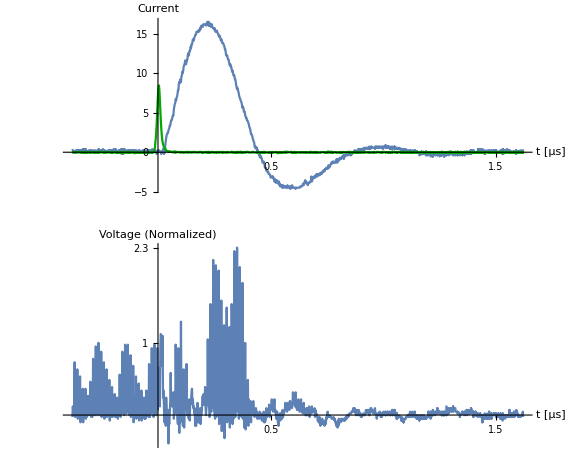

```mathematica
g2=GraphicsColumn[{
ListLinePlot[{Thread[{t,ch2}],Thread[{t,3ch1}]}
,AxesLabel->{"t [μs]","Current"}
,AxesStyle->axesStyle
,Ticks->{xTicks,Automatic}
,LabelStyle->Directive[Black,fontSize]
,PlotStyle->{Automatic,Darker[Green]}
,PlotRange->All
,AspectRatio->1/3]
,
ListLinePlot[Thread[{t,ch3}]
,AxesLabel->{"t [μs]","Voltage\n(Normalized)"}
,AxesStyle->axesStyle
,Ticks->{xTicks,{{Max[ch3⟦;;150⟧],1,dT,Black},{Max[ch3],NumberForm[Max[ch3]/Max[ch3⟦;;150⟧],2],dT,Black}}}
,LabelStyle->Directive[Black,fontSize]
,PlotRange->All
,AspectRatio->1/3]
},
GridLines->{Table[175+10i,{i,4}],None},GridLinesStyle->{{Dashed,Red},None},ImageSize->Large]
```

## 2020-02-02\RefCurve_130143.txt.Wfm

```mathematica
data=Import["guiding03.csv","Dataset",HeaderLines->1];
t=Normal[data[All,"t"]];
ch1=Normal[data[All,"ch1"]];
ch2=Normal[data[All,"ch2"]];
ch3=Normal[data[All,"ch3"]];
```

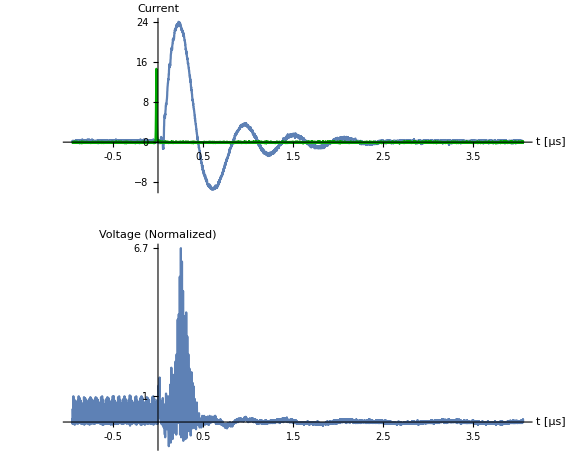

```mathematica
g3=GraphicsColumn[{
ListLinePlot[{Thread[{t,ch2}],Thread[{t,5RotateLeft[ch1,15]}]}
,AxesLabel->{"t [μs]","Current"}
,AxesStyle->axesStyle
,Ticks->{xTicks,Automatic}
,LabelStyle->Directive[Black,fontSize]
,PlotStyle->{Automatic,Darker[Green]}
,PlotRange->All
,AspectRatio->1/3]
,
ListLinePlot[Thread[{t,ch3}]
,AxesLabel->{"t [μs]","Voltage\n(Normalized)"}
,AxesStyle->axesStyle
,Ticks->{xTicks,{{Max[ch3⟦;;150⟧],1,dT,Black},{Max[ch3],NumberForm[Max[ch3]/Max[ch3⟦;;150⟧],2],dT,Black}}}
,LabelStyle->Directive[Black,fontSize]
,PlotRange->All
,AspectRatio->1/3]
},
GridLines->{Table[140+5i,{i,4}],None},GridLinesStyle->{{Dashed,Red},None},PlotRangePadding->0,ImageSize->Large]
```

```mathematica
Export["guiding1.pdf",Grid[{{g1},{g2}},Dividers->Center]]
Export["guiding2.pdf",g3]
```